# Part A: Harmonic Oscillator Wavefunctions

A1:
a)

```mathematica
α=m ω/ℏ;
normn[n_] := √(√α/(√π 2^n n!));
psi[x_,n_] := normn[n]*HermiteH[n, √α* x]*Exp[-α x^2/2];
Psi0[x_]:=psi[x,0];
Psi1[x_]:=psi[x,1];
Psi2[x_]:=psi[x,2];
Psi3[x_]:=psi[x,3];
```

The four lowest values are displayed above. Where Psi0[x_] is the ground state to the 3rd excited state of Psi3[x_]. Integrating over all space we found and displayed the normalized wavefunctions below.

```mathematica
Psi0[x]
Psi1[x]
Psi2[x]
Psi3[x]
(* Normalization below*)
Print[]
Integrate[Psi0[x]*Psi0[x],{x,-Infinity,Infinity}]
Integrate[Psi1[x]*Psi1[x],{x,-Infinity,Infinity}]
Integrate[Psi2[x]*Psi2[x],{x,-Infinity,Infinity}]
Integrate[Psi3[x]*Psi3[x],{x,-Infinity,Infinity}]
```

(ⅇ^(-(m x^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4))/π^(1/4)

(√2 ⅇ^(-(m x^2 ω)/(2 ℏ)) x ((m ω)/ℏ)^(3/4))/π^(1/4)

(ⅇ^(-(m x^2 ω)/(2 ℏ)) (-2+(4 m x^2 ω)/ℏ) ((m ω)/ℏ)^(1/4))/(2 √2 π^(1/4))

(ⅇ^(-(m x^2 ω)/(2 ℏ)) (-12 x √((m ω)/ℏ)+8 x^3 ((m ω)/ℏ)^(3/2)) ((m ω)/ℏ)^(1/4))/(4 √3 π^(1/4))

ConditionalExpression[1,Re[(m ω)/ℏ]>0]

ConditionalExpression[1,Re[(m ω)/ℏ]>0]

ConditionalExpression[1,Re[(m ω)/ℏ]>0]

«1 more identical outputs»

b)
Below are the Plots for the first 2 energy states. Notice we Plot (ψ_0)^2  and  (ψ_1)^2, therefore these plots are the probability distributions of the these energy levels. Where ψ_0 is red and ψ_1 is in blue.

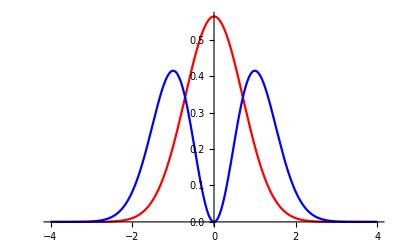

```mathematica
subs := {α->1, m->1, ω->1,ℏ->1}
Psi0[x_] = Psi0[x]/.subs;
Psi1[x_]=Psi1[x]/.subs;
Plot[{Psi0[x]*Psi0[x],Psi1[x]*Psi1[x]},{x,-4,4},PlotRange->Full, PlotStyle->{ Red,Blue}]
```

Including the imaginary components we plotted , ψ_0 as red and ψ_1 as blue below.

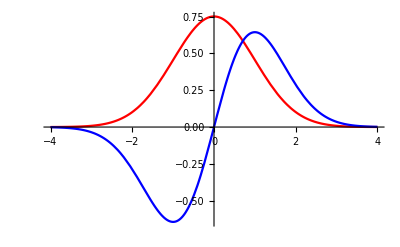

```mathematica
Plot[{Psi0[x],Psi1[x]},{x,-4,4},PlotRange->Full, PlotStyle->{ Red,Blue}]
```

c)
A plot of the potential energy and PDF was generated for the first 6 stationary wavefunctions. The energy of each state was shifted above by their respective energy using E = (n + 1/2), where n is the state.

{1/2+(ⅇ^(-x^2))/(√π),3/2+(2 ⅇ^(-x^2) x^2)/(√π),5/2+(ⅇ^(-x^2) (-2+4 x^2)^2)/(8 √π),7/2+(ⅇ^(-x^2) (-12 x+8 x^3)^2)/(48 √π),9/2+(ⅇ^(-x^2) (12-48 x^2+16 x^4)^2)/(384 √π),11/2+(ⅇ^(-x^2) (120 x-160 x^3+32 x^5)^2)/(3840 √π)}

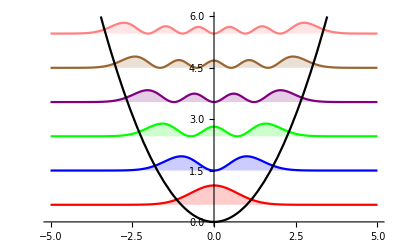

```mathematica
psii[x_,n_]:= psi[x,n]/.subs
wavefunctions := Table[psii[x,n]*psii[x,n]+n+1/2,{n,0,5}]
wavefunctions
Plot[{wavefunctions,x^2/2},{x,-5,5},Filling->Table[n->n-1/2,{n,1,6}],PlotRange->{0,6}, PlotStyle->{Red,Blue,Green,Purple,Brown,Pink,Black}]
```

A2:
a)
The amplitude is equal to Amplitude, and below we can see that it increases with energy.

```mathematica
Amplitude[n_] := Sqrt[(2*n+1)*ℏω/m *ω]
Amplitude[0]
Amplitude[1]
Amplitude[2]
```

√((ω ℏ)/m)

√3 √((ω ℏ)/m)

√5 √((ω ℏ)/m)

b)
Using E = K + U, where K = 1/2mv^2 and U = 1/2kx^2. We equated E(classic) with E = (n+1/2)ℏω. The velocity of the particle was obtained through algebra. Then the probability of finding the particle between [-A,A] was obtained by noticing the V= dx/dt, and justifying that the probability of finding a particle is dependent on the time that the particle spends in a given area. Therefore, Prob(finding x) = dt = 1/v.

1/(√(-m x^2 ω^2+((1+2 n) ω ℏ)/m))

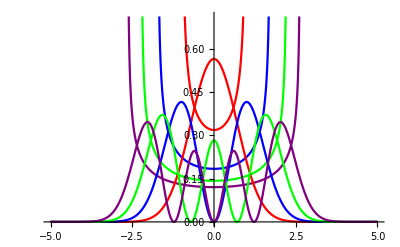

```mathematica
V[x_,n_] :=Sqrt[(2*n+1)/m *ℏ*ω - m*ω^2*x^2 ];
subs:={m->1,  ω->1, ℏ->1};
prob[x_,n_] = 1/V[x,n] (*Probability*)
(*In order to find out how the classical particle behaves we need to find the normalization constant in order to obtain our density function. We know that the particle has the amplidute defined in part a). The density function is equal to 1 , therefore a general PDF(X) = CONSTANT*Prob[x,n], where
Constant = 1/Integral[Prob[x],{x,-A,A}] *)

normalize[n_] :=1/Integrate[Simplify[prob[x,n]/.subs],{x,-Amplitude[n]/.subs,Amplitude[n]/.subs}]
(* General PDF for n energy state *)
pdfA2b [x_,n_] := normalize[n] * prob[x,n] /. subs
For[i = 0, i <4,i++,pdf[i] =pdfA2b[x,i]]
Plot[{pdf[0],pdf[1],pdf[2],pdf[3],psii[x,0]^2,psii[x,1]^2,psii[x,2]^2,psii[x,3]^2},{x,-5,5}
,PlotStyle->{Red,Blue,Green,Purple,Red, Blue, Green,Purple}]
```

The sharp peaks of the classical particle is due to the velocity of the particle being zero. Those are the classical turning points where all of the particles energy is in the potential energy. Since the plot above represents a probability density function, we see that at the ends of the oscillator the probability of finding a classical particle is significantly higher compared to a quantum particle.

c) 

A quantum particle reaches the classical limit when the spacing between energy levels is insignificant, this happens as energy is increased. Another way of looking at this argument is relating it back to the de Broglie equation and stating that the mass of a particle is what gives it his quantum behavior, a baseball behaves as a particle since its mass is not in the same order of magnitude as h unlike an electron. mass is directly related to kinetic energy which relates to the argument stated earlier, therefore to test this we created plots below of three different particles with high energy levels(n). It was found that at larger energy levels a quantum particle will behave like a classical particle by looking at the distribution as n is incremented by 30 starting a 5.

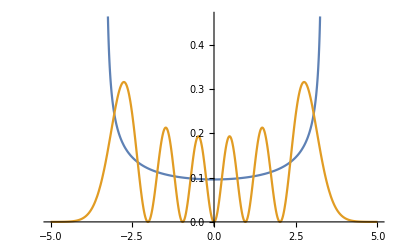

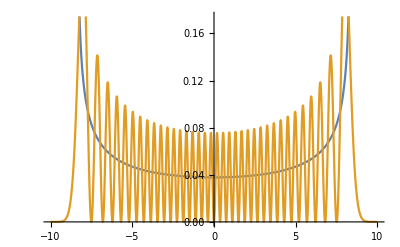

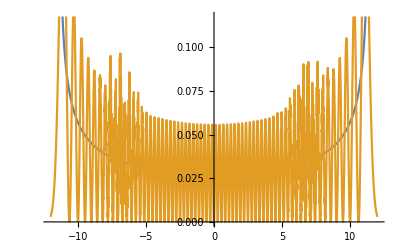

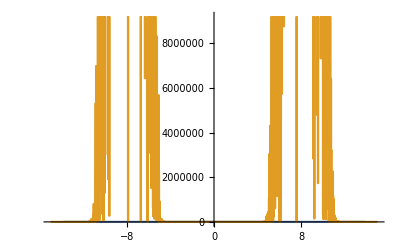

```mathematica
For[ i = 5,i < 100, i = i + 30 ,pdf2[i] = pdfA2b[x,i]]
Plot[{pdf2[5],psii[x,5]^2},{x,-5,5}] (* Energy state 5 pdf*)
Plot[{pdf2[35],psii[x,35]^2},{x,-10,10}] (* Energy state 35 pdf*)
Plot[{pdf2[65],psii[x,65]^2},{x,-12,12}](* Energy state 65 pdf*)
Plot[{pdf2[95],psii[x,95]^2},{x,-15,15}](* Energy state 95 pdf*)
```